# Taylor Series Error Assignment

### Instructions

The purpose of this assignment is to assess your ability to determine error bounds for Taylor polynomial approximations. Some things to remember as you complete this assignment:
1. Save the notebook to your computer right away, and save your work often. 
2. When you have finished all the exercises, close any unnecessary cells and save as a PDF.
3. Upload the PDF on Canvas.
4. Do not delete this notebook. Save all your work until after the semester is over and your final grade has been issued.

### Problem 1

Given the function f(x)=1/(√(x+4.5)), answer the following questions: 

a) Calculate the 6th degree Taylor polynomial centered at zero of the function and use it to approximate 1/(√2.5).

```mathematica
f[x_]=1/(√(x+4.5));
t[x_]=Normal[Series[f[x],{x,0,6}]];
t[2.5]
```

0.379026

b) Plot the absolute value of the 7th derivative of the function on the interval from -2 to -1, and find its maximum value, i.e. find M. Show your work or justify your answer. Store your final value as a decimal to “M”.

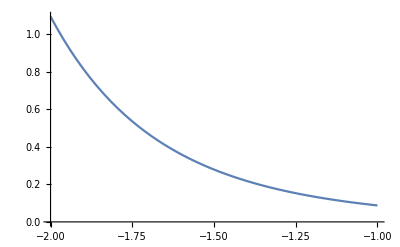

```mathematica
f7[x_]=D[f[x],{x,7}];
Plot[Abs[f7[x]],{x,-2,-1}]
```

The maximum value on the interval is at x = -2 so we will use that for M

```mathematica
Subscript[M, f] = Abs[f7[-2]]
```

1.09398

c) Calculate a bound for the error in your approximation over the interval -2 ≤ x ≤ -1.

```mathematica
Subscript[R, 6]=Subscript[M, f]/(7!)(Abs[-2])^7
```

0.0277835

d) Verify the error bound you just computed by plotting  |R_n(x)|=|f(x)-T_n(x)| along with your error bound for -2 ≤ x ≤ -1.  Is the exact error within your error bound over the entire interval?

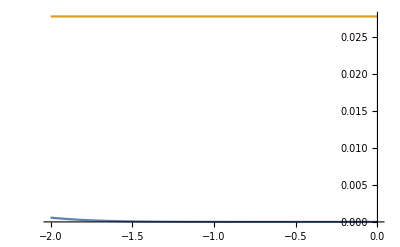

```mathematica
Plot[{f[x]-t[x],Subscript[R, 6]},{x,-2,-0}]
```

### Problem 2

Given the function g(x)=arctan(x)*x, answer the following questions:  

a) Calculate the 6th degree Taylor polynomial centered at zero of the function and use it to approximate arctan(0.4)*0.4.

```mathematica
g[x_]=ArcTan[x] x;
Subscript[t, g][x_]=Normal[Series[g[x],{x,0,6}]]
Subscript[t, g][.4]
```

x^2-x^4/3+x^6/5

0.152286

b) Plot the absolute value of the 7th derivative of the function on the interval from 0 to 0.4, and find its maximum value, i.e. find M. Show your work or justify your answer. Store your final value as a decimal to “M”.

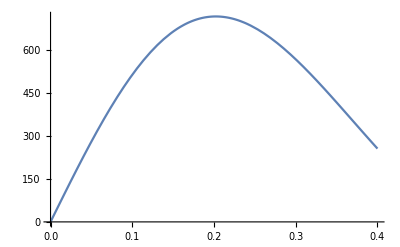

```mathematica
g7[x_]=D[g[x],{x,7}];
Plot[Abs[g7[x]],{x,0,.4}]
```

```mathematica
r=r/.FindRoot[g7'[r]==0,{r,.2}]
Subscript[M, g]=Abs[g7[r]]
```

0.202198

715.371

c) Calculate a bound for the error in your approximation over the interval 0 ≤ x ≤ 0.4.

```mathematica
R = Subscript[M, g]/(7!)Abs[.4]^7
```

0.000232552

d) Verify the error bound you just computed by plotting  |R_n(x)|=|g(x)-T_n(x)| along with your error bound for 0 ≤ x ≤ 0.4.  Is the exact error within your error bound over the entire interval?

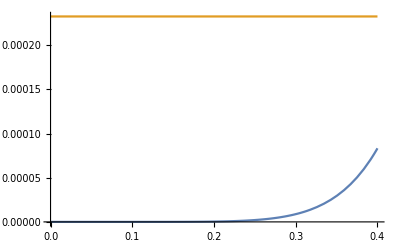

```mathematica
Plot[{Abs[g[x]-Subscript[t, g][x]],R},{x,0,.4}]
```